```mathematica
<<backprop1`
```

```mathematica
net:=NetInitialize@NetChain[
{
LinearLayer[1],
LogisticSigmoid,
LinearLayer[1]
},
"Input"->"Scalar",
"Output"->"Scalar"
];
```

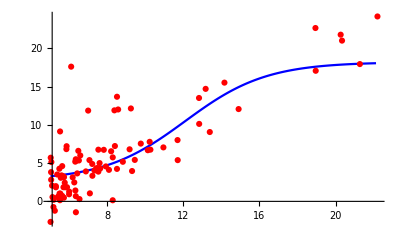

```mathematica
train[net,datum2]
```

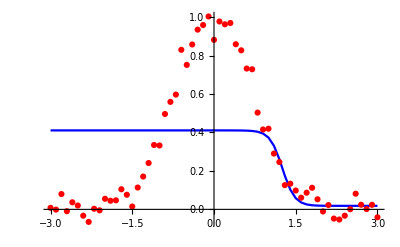

```mathematica
train[net,datumGaussian]
```

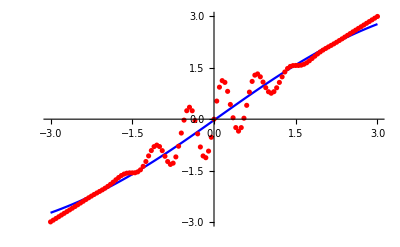

```mathematica
train[net,datumWavepacket]
```